```mathematica
Quit[]
```

### Packages

```mathematica
SetDirectory[NotebookDirectory[]];
<<MaTeX` (* Package to make plots with LaTeX fonts *)
```

# wCDM: Matter Power Spectrum

## ΛCDM Varying ω_m

```mathematica
ΛCDM.b4Files="/Users/cosmology/class_public/output/LCDM/";
```

```mathematica
PkΛCDM=Import[ΛCDM.b4Files<>"omega_cdm_LCDM_pk.dat","Data"][[5;;-1]]//Quiet;
Pkωc0.b411=Import[ΛCDM.b4Files<>"omega_cdm_0.11_pk.dat","Data"][[5;;-1]]//Quiet;
Pkωc0.b4115=Import[ΛCDM.b4Files<>"omega_cdm_0.115_pk.dat","Data"][[5;;-1]]//Quiet;
Pkωc0.b4125=Import[ΛCDM.b4Files<>"omega_cdm_0.125_pk.dat","Data"][[5;;-1]]//Quiet;
Pkωc0.b413=Import[ΛCDM.b4Files<>"omega_cdm_0.13_pk.dat","Data"][[5;;-1]]//Quiet;
```

```mathematica
(* Value of the normalization constant *)
PkΛCDM[[1,2]]/PkΛCDM[[1,1]]^0.965
```

3.10456×10^6

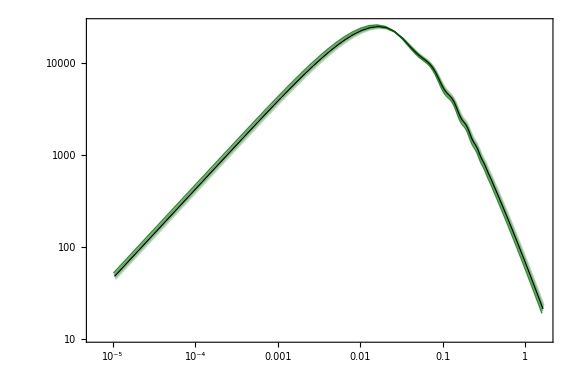

```mathematica
ListLogLogPlot[{Pkωc0.b411,Pkωc0.b4115,PkΛCDM,Pkωc0.b4125,Pkωc0.b413},Joined->True,PlotRange->All,PlotStyle->{Directive[RGBColor[0.1,0.5,0.1],Opacity[0.9],Thick],Directive[RGBColor[0.1,0.5,0.1],Opacity[0.7],Thick],Directive[Black,Thick],Directive[RGBColor[0.1,0.5,0.1],Opacity[0.5],Thick],Directive[RGBColor[0.1,0.5,0.1],Opacity[0.3],Thick]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [ (\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->18},PlotLegends->Placed[LineLegend[{
(MaTeX[#,Magnification->1.2]&)/@Style["\\omega_c = 0.11"],
(MaTeX[#,Magnification->1.2]&)/@Style["\\omega_c = 0.115"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\omega_c = 0.12"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\omega_c = 0.125"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\omega_c = 0.13"]},
 LegendLayout->{"Row", 3},LabelStyle->{Black,Bold,20},LegendMarkerSize->{25},LegendFunction->Frame],{0.57,0.3}],AspectRatio->0.65,ImageSize->Large]
```

## ΛCDM Varying n_s

```mathematica
PkΛCDM.b4ns=Partition[Import["Data_Pk_ns.txt","Data"],500];
```

```mathematica
ns.b4vals={0.96, 0.9625, 0.965 ,0.9675 ,0.97};
```

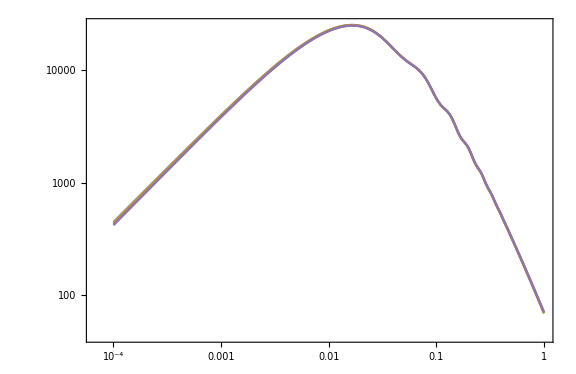

```mathematica
(* no modifications *)
ListLogLogPlot[{PkΛCDM.b4ns[[1]],PkΛCDM.b4ns[[2]],PkΛCDM.b4ns[[3]],PkΛCDM.b4ns[[4]],PkΛCDM.b4ns[[5]]},Joined->True,PlotRange->All,Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [ (\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->18},PlotLegends->Placed[LineLegend[{
(MaTeX[#,Magnification->1.2]&)/@Style["n_s = 0.96"],
(MaTeX[#,Magnification->1.2]&)/@Style["n_s = 0.9625"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["n_s = 0.965"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["n_s = 0.9675"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["n_s = 0.97"]},
 LegendLayout->{"Row", 3},LabelStyle->{Black,Bold,20},LegendMarkerSize->{25},LegendFunction->Frame],{0.54,0.3}],AspectRatio->0.65,ImageSize->Large]
```

## wCDM Varying w and fixed c_s^2

```mathematica
wCDMfiles="/Users/cosmology/class_public/output/wCDM/";
```

```mathematica
PkΛCDM=Import["/Users/cosmology/hi_class_public/output/lcdm_pk.dat","Data"][[5;;-1]]//Quiet;
Pkw08cs20001=Import[wCDMfiles<>"w_0.8_cs2_0.001_pk.dat","Data"][[5;;-1]]//Quiet;
Pkw09cs20001=Import[wCDMfiles<>"w_0.9_cs2_0.001_pk.dat","Data"][[5;;-1]]//Quiet;
Pkw1cs20001=Import[wCDMfiles<>"w_1_cs2_0.001_pk.dat","Data"][[5;;-1]]//Quiet;
Pkw11cs20001=Import[wCDMfiles<>"w_1.1_cs2_0.001_pk.dat","Data"][[5;;-1]]//Quiet;
Pkw12cs20001=Import[wCDMfiles<>"w_1.2_cs2_0.001_pk.dat","Data"][[5;;-1]]//Quiet;
```

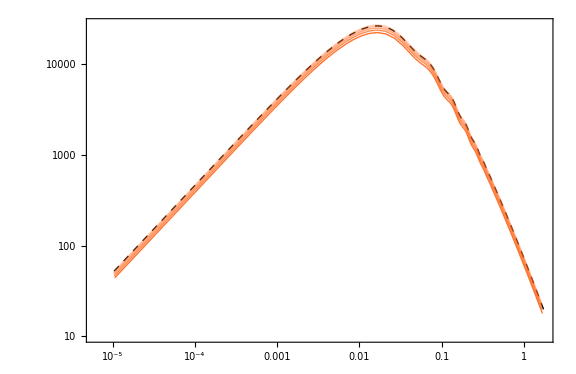

```mathematica
ListLogLogPlot[{PkΛCDM,Pkw08cs20001,Pkw09cs20001,Pkw1cs20001,Pkw11cs20001,Pkw12cs20001},Joined->True,PlotRange->All,PlotStyle->{Directive[Black,Dashed,Thick],Directive[RGBColor[1.0,0.4,0.1],Opacity[0.9],Thick],Directive[RGBColor[1.0,0.4,0.1],Opacity[0.75],Thick],Directive[RGBColor[1.0,0.4,0.1],Opacity[0.6],Thick],Directive[RGBColor[1.0,0.4,0.1],Opacity[0.45],Thick],Directive[RGBColor[1.0,0.4,0.1],Opacity[0.3],Thick],Directive[RGBColor[1.0,0.4,0.1],Opacity[0.15],Thick]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [ (\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->18},PlotLegends->Placed[LineLegend[{
(MaTeX[#,Magnification->1.2]&)/@Style["\\Lambda\\text{CDM}"],
(MaTeX[#,Magnification->1.2]&)/@Style["w = -0.8"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["w = -0.9"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["w = -1"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["w = -1.1"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["w = -1.2"]},
 LegendLayout->{"Row", 4},LabelStyle->{Black,Bold,20},LegendMarkerSize->{25},LegendFunction->Frame],{0.57,0.3}],AspectRatio->0.65,ImageSize->Large]
```

# EFT: Matter Power Spectrum

## propto_omega: α_i=(α̃)_i Ω_DE

## Braiding

```mathematica
Braiding.b4Files="/Users/cosmology/hi_class_public/output/propto_omega/Braiding/";
```

```mathematica
PkΛCDM=Import["/Users/cosmology/hi_class_public/output/lcdm_pk.dat","Data"][[5;;-1]]//Quiet;
PkB0=Import[Braiding.b4Files<>"B_0_pk.dat","Data"][[5;;-1]]//Quiet;
PkB0.b4625=Import[Braiding.b4Files<>"B_0.625_pk.dat","Data"][[5;;-1]]//Quiet;
PkB1.b425=Import[Braiding.b4Files<>"B_1.25_pk.dat","Data"][[5;;-1]]//Quiet;
PkB1.b4875=Import[Braiding.b4Files<>"B_1.875_pk.dat","Data"][[5;;-1]]//Quiet;
PkB2.b45=Import[Braiding.b4Files<>"B_2.5_pk.dat","Data"][[5;;-1]]//Quiet;
```

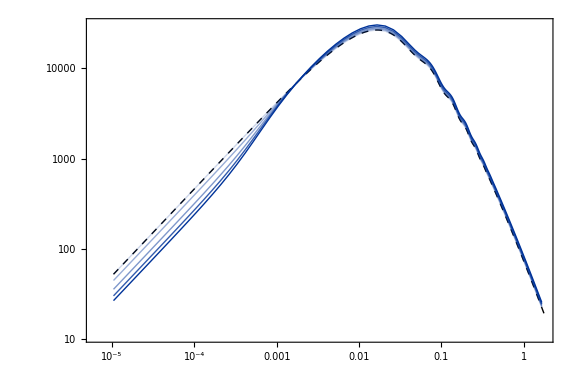

```mathematica
ListLogLogPlot[{PkΛCDM,PkB0,PkB0.b4625,PkB1.b425,PkB1.b4875,PkB2.b45},Joined->True,PlotRange->All,PlotStyle->{Directive[Black,Dashed,Thick],Directive[RGBColor[0,0.2,0.6],Opacity[0.2],Thick],Directive[RGBColor[0,0.2,0.6],Opacity[0.4],Thick],Directive[RGBColor[0,0.2,0.6],Opacity[0.5],Thick],Directive[RGBColor[0,0.2,0.6],Opacity[0.8],Thick],Directive[RGBColor[0,0.2,0.6],Thick]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [ (\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->18},PlotLegends->Placed[LineLegend[{
(MaTeX[#,Magnification->1.2]&)/@Style["\\Lambda\\text{CDM}"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\tilde{\\alpha}_B = 0"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\tilde{\\alpha}_B = 0.625"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\tilde{\\alpha}_B = 1.25"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\tilde{\\alpha}_B = 1.875"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\tilde{\\alpha}_B = 2.5"]},
 LegendLayout->{"Row", 3},LabelStyle->{Black,Bold,15},LegendMarkerSize->25,LegendFunction->Frame],{0.59,0.3}],AspectRatio->0.65,ImageSize->Large]
```

## Mass Running

```mathematica
Running.b4Files="/Users/cosmology/hi_class_public/output/propto_omega/Running/";
```

```mathematica
PkΛCDM=Import["/Users/cosmology/hi_class_public/output/lcdm_pk.dat","Data"][[5;;-1]]//Quiet;
PkM0=Import[Running.b4Files<>"M_0_pk.dat","Data"][[5;;-1]]//Quiet;
PkM1=Import[Running.b4Files<>"M_1_pk.dat","Data"][[5;;-1]]//Quiet;
PkM2=Import[Running.b4Files<>"M_2_pk.dat","Data"][[5;;-1]]//Quiet;
PkM3=Import[Running.b4Files<>"M_3_pk.dat","Data"][[5;;-1]]//Quiet;
PkM4=Import[Running.b4Files<>"M_4_pk.dat","Data"][[5;;-1]]//Quiet;
```

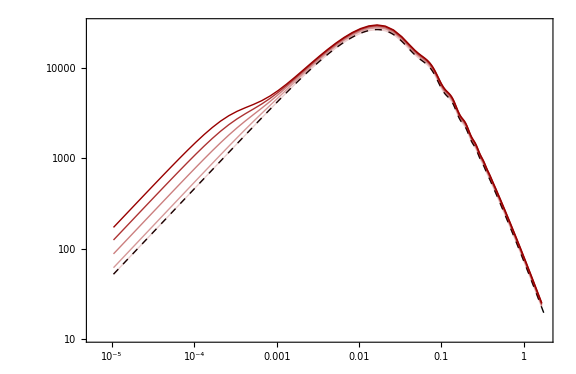

```mathematica
ListLogLogPlot[{PkΛCDM,PkM0,PkM1,PkM2,PkM3,PkM4},Joined->True,PlotRange->All,PlotStyle->{Directive[Black,Dashed,Thick],Directive[RGBColor[0.6,0,0],Opacity[0.2],Thick],Directive[RGBColor[0.6,0,0],Opacity[0.4],Thick],Directive[RGBColor[0.6,0,0],Opacity[0.5],Thick],Directive[RGBColor[0.6,0,0],Opacity[0.8],Thick],Directive[RGBColor[0.6,0,0],Thick]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [ (\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->18},PlotLegends->Placed[LineLegend[{
(MaTeX[#,Magnification->1.2]&)/@Style["\\Lambda\\text{CDM}"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\tilde{\\alpha}_M = 0"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\tilde{\\alpha}_M = 1"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\tilde{\\alpha}_M = 2"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\tilde{\\alpha}_M = 3"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\tilde{\\alpha}_M = 4"]},
 LegendLayout->{"Row", 3},LabelStyle->{Black,Bold,15},LegendMarkerSize->25,LegendFunction->Frame],{0.58,0.3}],AspectRatio->0.65,ImageSize->Large]
```

## Speed Excess

```mathematica
Excess.b4Files="/Users/cosmology/hi_class_public/output/propto_omega/Excess/";
```

```mathematica
PkΛCDM=Import["/Users/cosmology/hi_class_public/output/lcdm_pk.dat","Data"][[5;;-1]]//Quiet;
PkT0=Import[Excess.b4Files<>"T_0_pk.dat","Data"][[5;;-1]]//Quiet;
PkT0.b425=Import[Excess.b4Files<>"T_0.25_pk.dat","Data"][[5;;-1]]//Quiet;
PkT0.b45=Import[Excess.b4Files<>"T_0.5_pk.dat","Data"][[5;;-1]]//Quiet;
PkT0.b475=Import[Excess.b4Files<>"T_0.75_pk.dat","Data"][[5;;-1]]//Quiet;
PkT1=Import[Excess.b4Files<>"T_1_pk.dat","Data"][[5;;-1]]//Quiet;
```

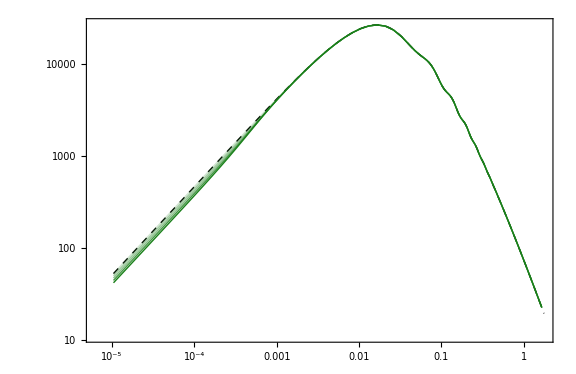

```mathematica
ListLogLogPlot[{PkΛCDM,PkT0,PkT0.b425,PkT0.b45,PkT0.b475,PkT1},Joined->True,PlotRange->All,PlotStyle->{Directive[Black,Dashed,Thick],Directive[RGBColor[0.1,0.5,0.1],Opacity[0.2],Thick],Directive[RGBColor[0.1,0.5,0.1],Opacity[0.4],Thick],Directive[RGBColor[0.1,0.5,0.1],Opacity[0.5],Thick],Directive[RGBColor[0.1,0.5,0.1],Opacity[0.8],Thick],Directive[RGBColor[0.1,0.5,0.1],Thick]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [ (\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->18},PlotLegends->Placed[LineLegend[{
(MaTeX[#,Magnification->1.2]&)/@Style["\\Lambda\\text{CDM}"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\tilde{\\alpha}_T = 0"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\tilde{\\alpha}_T = -0.25"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\tilde{\\alpha}_T = -0.5"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\tilde{\\alpha}_T = -0.75"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\tilde{\\alpha}_T = -1"]},
 LegendLayout->{"Row", 3},LabelStyle->{Black,Bold,15},LegendMarkerSize->25,LegendFunction->Frame],{0.58,0.3}],AspectRatio->0.65,ImageSize->Large]
```

## propto_scale: α_i=(α̂)_i a

## Braiding

```mathematica
Braiding.b4Files="/Users/cosmology/hi_class_public/output/propto_scale/Braiding/";
```

```mathematica
PkΛCDM=Import["/Users/cosmology/hi_class_public/output/lcdm_pk.dat","Data"][[5;;-1]]//Quiet;
PkB0=Import[Braiding.b4Files<>"B_0_pk.dat","Data"][[5;;-1]]//Quiet;
PkB0.b41=Import[Braiding.b4Files<>"B_0.1_pk.dat","Data"][[5;;-1]]//Quiet;
PkB0.b42=Import[Braiding.b4Files<>"B_0.2_pk.dat","Data"][[5;;-1]]//Quiet;
PkB0.b43=Import[Braiding.b4Files<>"B_0.3_pk.dat","Data"][[5;;-1]]//Quiet;
PkB0.b44=Import[Braiding.b4Files<>"B_0.4_pk.dat","Data"][[5;;-1]]//Quiet;
PkB0.b45=Import[Braiding.b4Files<>"B_0.5_pk.dat","Data"][[5;;-1]]//Quiet;
PkB0.b46=Import[Braiding.b4Files<>"B_0.6_pk.dat","Data"][[5;;-1]]//Quiet;
```

```mathematica
ListLogLogPlot[{PkΛCDM,PkB0.b41,PkB0.b42,PkB0.b43,PkB0.b44,PkB0.b45},Joined->True,PlotRange->All,PlotStyle->{Directive[Black,Dashed,Thick],Directive[RGBColor[0,0.2,0.6],Opacity[0.2],Thick],Directive[RGBColor[0,0.2,0.6],Opacity[0.4],Thick],Directive[RGBColor[0,0.2,0.6],Opacity[0.6],Thick],Directive[RGBColor[0,0.2,0.6],Opacity[0.8],Thick],Directive[RGBColor[0,0.2,0.6],Opacity[10],Thick]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [ (\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->18},PlotLegends->Placed[LineLegend[{
(MaTeX[#,Magnification->1.2]&)/@Style["\\Lambda\\text{CDM}"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_B = 0.1"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_B = 0.2"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_B = 0.3"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_B = 0.4"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_B = 0.5"]},
 LegendLayout->{"Row", 4},LabelStyle->{Black,Bold,20},LegendMarkerSize->{25},LegendFunction->Frame],{0.58,0.3}],AspectRatio->0.65,ImageSize->Large]
```

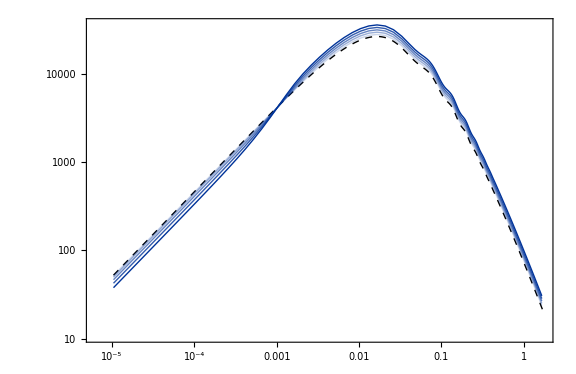

## Mass Running

```mathematica
Running.b4Files="/Users/cosmology/hi_class_public/output/propto_scale/Running/";
```

```mathematica
PkΛCDM=Import["/Users/cosmology/hi_class_public/output/lcdm_pk.dat","Data"][[5;;-1]]//Quiet;
PkM0=Import[Running.b4Files<>"M_0_pk.dat","Data"][[5;;-1]]//Quiet;
PkM0.b425=Import[Running.b4Files<>"M_0.25_pk.dat","Data"][[5;;-1]]//Quiet;
PkM0.b45=Import[Running.b4Files<>"M_0.5_pk.dat","Data"][[5;;-1]]//Quiet;
PkM0.b475=Import[Running.b4Files<>"M_0.75_pk.dat","Data"][[5;;-1]]//Quiet;
PkM1=Import[Running.b4Files<>"M_1_pk.dat","Data"][[5;;-1]]//Quiet;
```

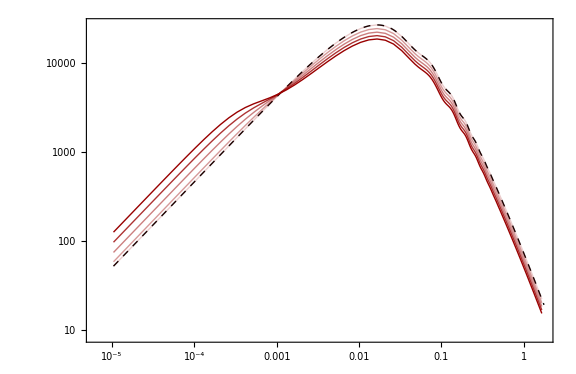

```mathematica
ListLogLogPlot[{PkΛCDM,PkM0,PkM0.b425,PkM0.b45,PkM0.b475,PkM1},Joined->True,PlotRange->All,PlotStyle->{Directive[Black,Dashed,Thick],Directive[RGBColor[0.6,0,0],Opacity[0.2],Thick],Directive[RGBColor[0.6,0,0],Opacity[0.4],Thick],Directive[RGBColor[0.6,0,0],Opacity[0.5],Thick],Directive[RGBColor[0.6,0,0],Opacity[0.8],Thick],Directive[RGBColor[0.6,0,0],Thick]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [ (\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->18},PlotLegends->Placed[LineLegend[{
(MaTeX[#,Magnification->1.2]&)/@Style["\\Lambda\\text{CDM}"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_M = 0"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_M = 0.25"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_M = 0.5"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_M = 0.75"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_M = 1"]},
 LegendLayout->{"Row", 3},LabelStyle->{Black,Bold,20},LegendMarkerSize->25,LegendFunction->Frame],{0.57,0.3}],AspectRatio->0.65,ImageSize->Large]
```

## Speed Excess

```mathematica
Excess.b4Files="/Users/cosmology/hi_class_public/output/propto_scale/Excess/";
```

```mathematica
PkΛCDM=Import["/Users/cosmology/hi_class_public/output/lcdm_pk.dat","Data"][[5;;-1]]//Quiet;
PkT0=Import[Excess.b4Files<>"T_0_pk.dat","Data"][[5;;-1]]//Quiet;
PkT0.b425=Import[Excess.b4Files<>"T_0.25_pk.dat","Data"][[5;;-1]]//Quiet;
PkT0.b45=Import[Excess.b4Files<>"T_0.5_pk.dat","Data"][[5;;-1]]//Quiet;
PkT0.b475=Import[Excess.b4Files<>"T_0.75_pk.dat","Data"][[5;;-1]]//Quiet;
PkT1=Import[Excess.b4Files<>"T_1_pk.dat","Data"][[5;;-1]]//Quiet;
```

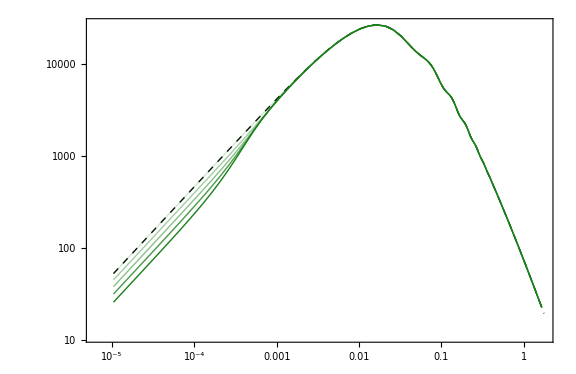

```mathematica
ListLogLogPlot[{PkΛCDM,PkT0,PkT0.b425,PkT0.b45,PkT0.b475,PkT1},Joined->True,PlotRange->All,PlotStyle->{Directive[Black,Dashed,Thick],Directive[RGBColor[0.1,0.5,0.1],Opacity[0.2],Thick],Directive[RGBColor[0.1,0.5,0.1],Opacity[0.4],Thick],Directive[RGBColor[0.1,0.5,0.1],Opacity[0.5],Thick],Directive[RGBColor[0.1,0.5,0.1],Opacity[0.8],Thick],Directive[RGBColor[0.1,0.5,0.1],Thick]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [ (\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->18},PlotLegends->Placed[LineLegend[{
(MaTeX[#,Magnification->1.2]&)/@Style["\\Lambda\\text{CDM}"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_T = 0"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_T = -0.25"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_T = -0.5"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_T = -0.75"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_T = -1"]},
 LegendLayout->{"Row", 3},LabelStyle->{Black,Bold,15},LegendMarkerSize->25,LegendFunction->Frame],{0.58,0.3}],AspectRatio->0.65,ImageSize->Large]
```

# Slips: Matter Power Spectrum

## plk_late: f_i=E_ii Ω_DE

```mathematica
(* Import datasets *)
plk.b4Files="/Users/cosmology/mgclass--ii/output/plk_late/";
PkE110.b4E220=Import[plk.b4Files<>"E11_0_E22_0_pk.dat","Data"][[7;;-1]]//Quiet;
PkE111.b4E221=Import[plk.b4Files<>"E11_1_E22_1_pk.dat","Data"][[7;;-1]]//Quiet;
PkE111n.b4E221n=Import[plk.b4Files<>"E11_1n_E22_1n_pk.dat","Data"][[7;;-1]]//Quiet;
PkE1105.b4E2205=Import[plk.b4Files<>"E11_0.5_E22_0.5_pk.dat","Data"][[7;;-1]]//Quiet;
PkE1105n.b4E2205n=Import[plk.b4Files<>"E11_0.5n_E22_0.5n_pk.dat","Data"][[7;;-1]]//Quiet;
PkE110.b4E221=Import[plk.b4Files<>"E11_0_E22_1_pk.dat","Data"][[7;;-1]]//Quiet;
```

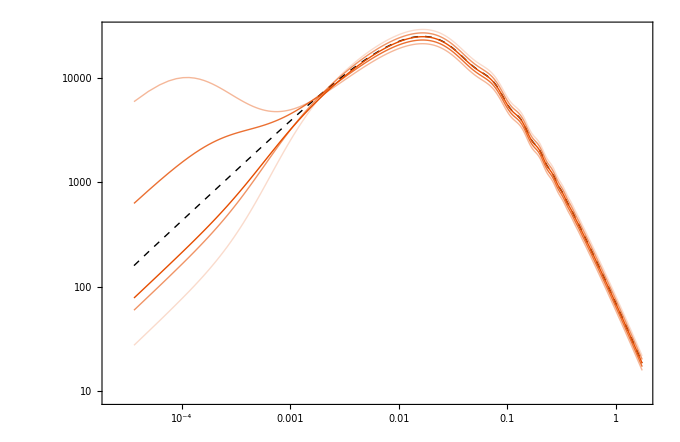

```mathematica
ListLogLogPlot[{PkE110.b4E220,PkE111.b4E221,PkE111n.b4E221n,PkE1105.b4E2205,PkE1105n.b4E2205n,PkE110.b4E221},Joined->True,PlotRange->All,PlotStyle->{Directive[Black,Dashed,Thick],Directive[RGBColor[0.9,0.3,0.0],Opacity[0.2],Thick],Directive[RGBColor[0.9,0.3,0.0],Opacity[0.4],Thick],Directive[RGBColor[0.9,0.3,0.0],Opacity[0.6],Thick],Directive[RGBColor[0.9,0.3,0.0],Opacity[0.8],Thick],Directive[RGBColor[0.9,0.3,0.0],Opacity[1],Thick]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [ (\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->18},PlotLegends->Placed[LineLegend[{
(MaTeX[#,Magnification->1.2]&)/@Style["\\Lambda\\text{CDM}"],
(MaTeX[#,Magnification->1.2]&)/@Style["E_{11} = 1, \\quad E_{22} = 1"],
(MaTeX[#,Magnification->1.2]&)/@Style["E_{11} = -1, \\quad E_{22} = -1"],
(MaTeX[#,Magnification->1.2]&)/@Style["E_{11} = 0.5, \\quad E_{22} = 0.5"],
(MaTeX[#,Magnification->1.2]&)/@Style["E_{11} = -0.5, \\quad E_{22} = -0.5"],
(MaTeX[#,Magnification->1.2]&)/@Style["E_{11} = 0, \\quad E_{22} = 1"]},
 LegendLayout->{"Row", 6},LabelStyle->{Black,Bold,15},LegendMarkerSize->25,LegendFunction->Frame],{0.56,0.35}],AspectRatio->0.65,ImageSize->680]
```